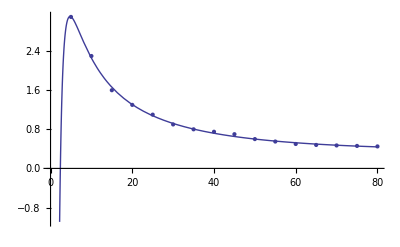

-0.0556334-72.2653/x^2+30.2105/x+0.00162233 x

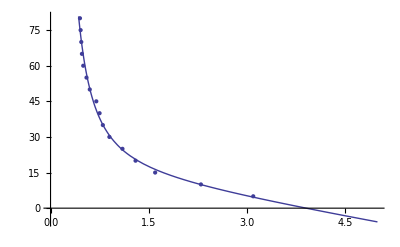

16.6729+9.78139/x^2+5.61461/x-4.79446 x

```mathematica
data={{5,3.1},{10,2.3},{15,1.6},{20,1.3},{25,1.1},{30,0.9},{35,0.8},{40,0.75},{45,0.7},{50,0.6},{55,0.55},{60,0.5},{65,0.48},{70,0.47},{75,0.46},{80,0.45}};
dataInv={{3.1,5},{2.3,10},{1.6,15},{1.3,20},{1.1,25},{0.9,30},{0.8,35},{0.75,40},{0.7,45},{0.6,50},{0.55,55},{0.5,60},{0.48,65},{0.47,70},{0.46,75},{0.45,80}};
gp=ListPlot[data];
f=Fit[data,{x,1,1/x, 1/x^2},x];
Plot[%,{x,0,80}];
Show[%,gp]
f
gp=ListPlot[dataInv];
f=Fit[dataInv,{x^2,x,1,1/x,1/x^2},x];
Plot[%,{x,0,5}];
Show[%,gp]
f
```